## Bayesian Statistics, Exam 2

## Tuesday, Nov. 12, 2024 — Frequentist and Bayesian Statistics

## 1. χ^2 (3 pts)

In the mythical State of New Provence, an election is being held, and the results from the last 5 polls for the State Senator seat are:

```mathematica
pollingData ={{"Oct. 9", 409, 391},{"Oct. 11", 393, 407},{"Oct. 19", 395, 405},{"Oct. 24", 406, 394}, {"Oct. 29", 397, 403}};
TableForm[pollingData, TableHeadings->{None, {"Poll date", "Supports Girard", "Supports Reynaud"} }]
```

Poll date | Supports Girard | Supports Reynaud
Oct. 9 | 409 | 391
Oct. 11 | 393 | 407
Oct. 19 | 395 | 405
Oct. 24 | 406 | 394
Oct. 29 | 397 | 403

(a) Take the mean of these five polls, and report that. Also notice that each poll has a total of 800 respondents. What fraction of the vote total do you predict Girard will get?

HINT 1: The poll dates were included, but do not matter. I am not looking for any trend analysis. HINT 2: The Reynaud support numbers were tabulated, but they also don’t matter. They were only included to show that the total number of respondents was 800.

mean of Girard polls =


fraction of respondents =

(b) The election appears too close to call, and this certainly keeps both the Girard and Reynaud supporters anxiously buying papers for all of October. But you suspect that the paper or the pollsters are fabricating the numbers. Your suspicion centers on the fact that the variance in a Poisson distribution whose mean you found in (a) should be ______________, and the numbers in the five supposedly-independent polls look too closely clustered around the mean. Fill in the number in the blank. If you no longer remember the shockingly simple relationship between mean and variance for Poisson distributions, on the following page is the entire discussion from Young.
-Graphics-

## 1. (CONT’D)

To continue, you again consult your trusty copy of Statistical Treatment of Experimental Data by Hugh Young. He discusses the motivation for the definition of χ^2 on p. 82. The upshot of the discussion for our polling problem is:

χ^2≡∑_(i=1)^5 (residual_i)^2/variance

where

residual_i≡poll_i-mean

(c) In the space below, tabulate the 5 residuals, and in another column, tabulate their squares:








HINT/CROSS-CHECK: Residuals are both positive or negative, and the total of the residuals must add up to 0.

(d) Sum the squares, and then divide by the expected variance that you found in (b).








(e) The expected χ^2 for 5 data points with a fitted mean is 5-1=4. What does your answer to (d) tell you about the pollsters and the papers?

## 2. Dose-Response Relationship (3 pts)

This is a grisly subject, but it is important. A July 1961 paper by A.C. Upton in the journal Cancer Research summarized 23 cases of leukemia from 1950 to 1957 among people living near the Hiroshima atomic bomb explosion. Table 1 in the paper grouped the survivors into their distance from the explosion, tabulated the estimated radiation doses (in an old unit of exposure called the “rad”), and correlated this with the leukemia incidence rate (in cases per million people per year). Table 1 contains:

```mathematica
doseResponseData ={
{2620, 1790},{1060, 950},{430, 355},{177, 230},{77, 69},{34, 0},{19, 0}};
TableForm[doseResponseData, TableHeadings->{None, {"Dose, d_i", "Rate, r_i"}}]
```

Dose, d_i | Rate, r_i
2620 | 1790
1060 | 950
430 | 355
177 | 230
77 | 69
34 | 0
19 | 0

(a) We are going to use the simplest possible model: r=s·d. To get the slope, s, in this model you have to calculate:

A_2=∑_(i=1)^N d_i^2=2620^2+1060^2+430^2+177^2+77^2+34^2+19^2=8211675


A_1=∑_(i=1)^N r_i d_i=


I did A_2 for you already. Write out what A_1 is and then punch it into your calculator to get a total.

(b) The formula for s is below. Round A_1 to A_2 each to the nearest million, and then compute s:

s=A_1/A_2=


The units are leukemias cases per million people per year per rad.

HINT/CROSS-CHECK: Eye-balling the data, it looks like s is somewhat but not a lot less than 1.

## 3. Potato Harvesting — Compounded (4 pts)

Desperate to reduce the number of rocks being sent to the kitchen, the hungry village decides to send the nodules from the field through the potato harvester twice. In other words, instead of sending what the harvester would send straight to the kitchen, ... , what would have gone to the kitchen gets put through the harvester a second time.

Let us first figure out what happens on the first pass through the harvester. Here are the numbers you need: 20,000 nodules were harvested from the field. The field contains 9x as many rocks as potatoes. Of the potatoes, 95% get sorted correctly. Of the rocks, unfortunately, 20% of those get sorted incorrectly.

(a) Make a conjoint table whose margins add up to 20000. Fill in the seven blanks.

```mathematica
firstPassValues = {"",2000,20000};
data=Table[If[i==3, firstPassValues[[j]], "              "],{i,3},{j,3}];
table1 = Prepend[data, {"Is a Rock", "Is a Potato", "Is a Nodule"}];
table2 = MapThread[Prepend,{table1, {"","Discarded in First Pass", "Would have gone to Kitchen", "Sum"}}];
Grid[table2, Frame->All]
```

| Is a Rock | Is a Potato | Is a Nodule
Discarded in First Pass |                |                |               
Would have gone to Kitchen |                |                |               
Sum |  | 2000 | 20000

(b) Focus on the row above titled “Would have gone to Kitchen.” We are going to stick those nodules back into the same potato harvester for a second sorting. So that row is going to become the bottom row in the new table! Just copy that row over to the new table. Then fill in the remaining six blanks.

```mathematica
values = {"", 1900, 5500};
data=Table[If[i==3, values[[j]], "              "],{i,3},{j,3}];
table1 = Prepend[data, {"Is a Rock", "Is a Potato", "Is a Nodule"}];
table2 = MapThread[Prepend,{table1, {"","Discarded in Second Pass", "Sent to Kitchen", "Sum"}}];
Grid[table2, Frame->All]
```

| Is a Rock | Is a Potato | Is a Nodule
Discarded in Second Pass |                |                |               
Sent to Kitchen |                |                |               
Sum |  | 1900 | 5500

(c) In the field before harvesting, the fraction of nodules that were potatoes was 2000/20000 = 0.10 or 10%. After the first pass through the harvester, the fraction of nodules that were potatoes rose to 1900/5500 = 0.35 or 35%. Using the “Sent to Kitchen” row, what fraction of the nodules are potatoes after the second pass through the harvester? What is this as a percentage? Two sig figs is good.

## 4. The Mug Breakage Problem — But with an Exponential Prior (5 pts)

First we’ll calculate some likelihoods. Act as if a were known. (Remember the “likelihood” is by definition P(data|a). That means we are pretending that a is given.) The formula you need to get the likelihood was on p. 59 of Young.

-Graphics-

(a) Write down the likelihood of having 1 mug broken in the first week.

(b) Repeat, but with n=3 for the second week.

(c) Repeat, but with n=2 for the third week.

(d) Take the product of what you got in (a), (b), and (c). This is the joint likelihood of getting these three weeks of data.

P(data|a)=


(e) In Problem Set 11, we had one of those boxcar-shaped priors. In this problem, we are going to have an exponential prior: 

P(a)=2 e^(-2a)

The formula for the posterior is: P(a|data)=(P(data|a) * P(a))/(∫_0^∞ P(data|a) * P(a)da). For this part, we will just deal with the numerator. Then in the next part, we will deal with the denominator. Simplify the numerator as much as you can


P(data|a) * P(a)=




(f) I am going to have Mathematica plot the function that you got in the previous part. And I am going to have Mathematica do the integral in the denominator.

```mathematica
likelihood[a_]:=a^6 Exp[-3a]/12;
prior[a_]:=2Exp[-2a];
```

0.0015

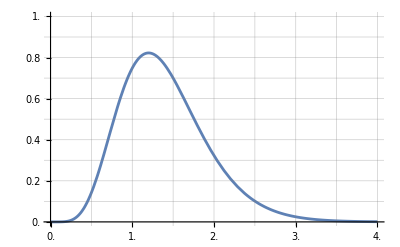

```mathematica
denominator = Round[Integrate[likelihood[a]*prior[a], {a, 0, Infinity}],0.0001]
Plot[likelihood[a]prior[a]/denominator,{a, 0, 4}, PlotRange->{{0, 4},{0,1}}, Ticks->{Range[0,4,0.5], Range[0.0,1,0.1]}, GridLines->{Range[0,4,0.5], Range[0.0,1,0.1]}]
```

So what does that leave you to do for this part!? Interpretation! Clearly the most probable mug breakage rate is somewhere between 1 and 1.5, but lots of other ranges of a are still non-negligible. Shade the region of the graph that tells you the probability that the mug breakage rate is between 2 and 2.5.

(g) Now that you have shaded the region of the graph that tells you the mug breakage rate is between 2 and 2.5, what is its width, what is its average height, and what is its area? When you are estimating the average height, one decimal place is plenty good for our purposes.




(h) Convert the area that you got in the previous part to a percentage.


I HOPE THIS EXAM WAS FUN! It was fun for me to write, because all of you are getting to the point that we can do problems quite similar to problems that matter in the real world. Each of these problems is building my intuition too!

Name ______________________________________

1.              / 3
2.              / 3
3.              / 4
4.              / 5

TOTAL          / 15